## Plotting functions given output of GeomComp_Compute.nb

## Preliminaries

```mathematica
Clear["Global`*"]
SetDirectory[FileNameJoin[{NotebookDirectory[],"results/"}]] ;
files=FileNames["P*.txt"] (* Get list of all result files *)
Get[#]&/@files; (* Load all their contents (variable definitions) *)
SetDirectory[FileNameJoin[{NotebookDirectory[],"../figs/"}]] ;
```

{P1fixH1.txt,P1fixLR.txt,P1varH1.txt,P1varLR.txt,P2fixA1.txt,P2fixA3.txt,P2fixAG.txt,P2fixGIA.txt,P2fixGI.txt,P2fixH2.txt,P2fixH3.txt,P2fixHT.txt,P2fixHV.txt,P2fixSH.txt,P2varA1.txt,P2varA3.txt,P2varAG.txt,P2varGIA.txt,P2varGI.txt,P2varH2.txt,P2varH3.txt,P2varHT.txt,P2varHV.txt,P2varSH.txt,P3fixA2.txt,P3fixAA.txt,P3fixBD.txt,P3fixBWL.txt,P3fixCM.txt,P3fixH3R.txt,P3fixHLB.txt,P3fixMH.txt,P3fixSSS.txt,P3fixTTA.txt,P3varA2.txt,P3varAA.txt,P3varBD.txt,P3varBWL.txt,P3varCM.txt,P3varH3R.txt,P3varHLB.txt,P3varMH.txt,P3varSSS.txt,P3varTTA.txt,P4varSN1.txt,P4varSN2.txt}

The data files each have four independent variables (Νmax, Pmax, number of prey levels, number of pred levels) and one response variable (volume = geometric complexity).

```mathematica
varH1//TableForm
```

21 | 2 | 5 | 2 | 1.31114
21 | 3 | 5 | 3 | 1.14654
34 | 2 | 6 | 2 | 1.56653
34 | 3 | 6 | 3 | 1.43309
55 | 2 | 7 | 2 | 1.81369
55 | 3 | 7 | 3 | 1.70024
89 | 2 | 8 | 2 | 2.04626
89 | 3 | 8 | 3 | 1.94693
144 | 2 | 9 | 2 | 2.26974
144 | 3 | 9 | 3 | 2.18036
233 | 2 | 10 | 2 | 2.49
233 | 3 | 10 | 3 | 2.40789

### Convenience function to append relative (ratios of) complexity values to independent variables

Denom_ is the measure to which the Numer_ measure is relativized.

```mathematica
Relativize[dataDenom_,dataNumer_]:=Join[dataNumer[[All,{1,2,3,4}]],Transpose[{dataNumer[[All,5]]/dataDenom[[All,5]]}],2];
```

```mathematica
PlotStyleCols={
{GrayLevel[0]},
{GrayLevel[0.7],Dashed}
};

MyListLinePlot[
data_,
predVars_,
axislabels_,
plotlabel_,
plotRange_]:=
ListLinePlot[
Transpose[SplitBy[data,Part[#,predVars[[1]]]&][[All,All,{predVars[[1]],5}]]],
ScalingFunctions->{"Log","Log"}, 
GridLines->{None,{1}},GridLinesStyle->Directive[LightGray, Dashed], (* horizontal line at 1 *)
PlotRange->plotRange,
PlotLegends->False,
Frame-> True,
PlotStyle->PlotStyleCols,
FrameLabel-> axislabels,
PlotLabel->plotlabel]
```

## Plot ratio of Geometric complexities - varying max abundance levels

```mathematica
axislabelsLineComp={"Max. prey abundance","Flexibility"};
axislabelsLineRel={"Max. prey abundance","Relative flexibility"};
axislabelsLineComp2={"Max. prey abundance",""};
axislabelsLineRel2={"Max. prey abundance",""};
```

#### k = 1 models

```mathematica
p1varH1=MyListLinePlot[
varH1,
{1,2},
axislabelsLineComp,
"H1",
{All,All}
];
p1varH1vLR=MyListLinePlot[
Relativize[varH1,varLR],
{1,2},
axislabelsLineRel,
"LR/H1",
{All,All}
];
```

#### k = 2 models

```mathematica
p2varH2=MyListLinePlot[
varH2,
{1,2},
axislabelsLineComp,
"H2",
{All,All}
];
p2varH2vHV=MyListLinePlot[
Relativize[varH2,varHV],
{1,2},
axislabelsLineRel,
"HV/H2",
{All,All}
];
p2varH2vAG=MyListLinePlot[
Relativize[varH2,varAG],
{1,2},
axislabelsLineRel,
"AG/H2",
{All,All}
];
p2varH2vGI=MyListLinePlot[
Relativize[varH2,varGI],
{1,2},
axislabelsLineRel,
"GI/H2",
{All,All}
];
p2varH2vGIA=MyListLinePlot[
Relativize[varH2,varGIA],
{1,2},
axislabelsLineRel,
"GIA/H2",
{All,All}
];
p2varH2vHT=MyListLinePlot[
Relativize[varH2,varHT],
{1,2},
axislabelsLineRel,
"HT/H2",
{All,All}
];
p2varH2vH3=MyListLinePlot[
Relativize[varH2,varH3],
{1,2},
axislabelsLineRel,
"H3/H2",
{All,All}
];
p2varH2vA1=MyListLinePlot[
Relativize[varH2,varA1],
{1,2},
axislabelsLineRel,
"A1/H2",
{All,All}
];
p2varH2vA3=MyListLinePlot[
Relativize[varH2,varA3],
{1,2},
axislabelsLineRel,
"A3/H2",
{All,All}
];
p2varH2vSH=MyListLinePlot[
Relativize[varH2,varSH],
{1,2},
axislabelsLineRel,
"SH/H2",
{All,All}
];
```

#### k = 3 models

```mathematica
p3varBD=MyListLinePlot[
varBD,
{1,2},
axislabelsLineComp,
"BD",
{All,All}
];
p3varBDvCM=MyListLinePlot[
Relativize[varBD,varCM],
{1,2},
axislabelsLineRel,
"CM/BD",
{All,All}
];
p3varBDvAA=MyListLinePlot[
Relativize[varBD,varAA],
{1,2},
axislabelsLineRel,
"AA/BD",
{All,All}
];
p3varBDvBWL=MyListLinePlot[
Relativize[varBD,varBWL],
{1,2},
axislabelsLineRel,
"BWL/BD",
{All,All}
];
p3varBDvH3R=MyListLinePlot[
Relativize[varBD,varH3R],
{1,2},
axislabelsLineRel,
"H3R/BD",
{All,All}
];
p3varBDvA2=MyListLinePlot[
Relativize[varBD,varA2],
{1,2},
axislabelsLineRel,
"A2/BD",
{All,All}
];
p3varBDvHLB=MyListLinePlot[
Relativize[varBD,varHLB],
{1,2},
axislabelsLineRel,
"HLB/BD",
{All,All}
];
p3varBDvMH=MyListLinePlot[
Relativize[varBD,varMH],
{1,2},
axislabelsLineRel,
"MH/BD",
{All,All}
];
p3varBDvTTA=MyListLinePlot[
Relativize[varBD,varTTA],
{1,2},
axislabelsLineRel,
"TTA/BD",
{All,All}
];
p3varBDvSSS=MyListLinePlot[
Relativize[varBD,varSSS],
{1,2},
axislabelsLineRel,
"SSS/BD",
{All,All}
];
```

```mathematica
PlotStyleCols
```

{{GrayLevel[0]},{GrayLevel[0.7],Dashing[{Small,Small}]}}

#### Combined plots - Var

```mathematica
LineLegend[
Map[Directive,PlotStyleCols],
DeleteDuplicates[varH1[[All,2]]]
]
```

```mathematica
AllVarP1=
Legended[
GraphicsGrid[{
{p1varH1},
{p1varH1vLR}},
ImageSize-> Medium],
Placed[
LineLegend[
Map[Directive,PlotStyleCols],
DeleteDuplicates[varH1[[All,2]]],
LegendLabel->"Max. predator abundance",
LegendLayout->"Row"],
Above]];
Export["GeomComp_varP1.pdf",AllVarP1];
```

```mathematica
AllVarP2=
Legended[
GraphicsGrid[{
{p2varH2,p2varH2vHV,p2varH2vAG},
{p2varH2vGI,p2varH2vGIA,p2varH2vHT},
{p2varH2vH3,p2varH2vA1,p2varH2vA3},
{p2varH2vSH}
},
ImageSize-> Large],
Placed[
LineLegend[
Map[Directive,PlotStyleCols],
DeleteDuplicates[varH1[[All,2]]],
LegendLabel->"Max. predator abundance",
LegendLayout->"Row"],
Above]];
Export["GeomComp_varP2.pdf",AllVarP2];
```

```mathematica
AllVarP3=
Legended[
GraphicsGrid[{
{p3varBD,p3varBDvCM,p3varBDvAA},
{p3varBDvBWL,p3varBDvH3R,p3varBDvA2},
{p3varBDvHLB,p3varBDvMH,p3varBDvTTA},
{p3varBDvSSS}
},
ImageSize-> Large],
Placed[
LineLegend[
Map[Directive,PlotStyleCols],
DeleteDuplicates[varH1[[All,2]]],
LegendLabel->"Max. predator abundance",
LegendLayout->"Row"],
Above]];
Export["GeomComp_varP3.pdf",AllVarP3];
```

## Plot ratio of Geometric complexities - fixed max abundance levels

```mathematica
axislabelsLineComp={"Prey levels","Flexibility"};
axislabelsLineRel={"Prey levels","Relative flexibility"};
axislabelsLineComp2={"Prey levels",""};
axislabelsLineRel2={"Prey levels",""};
```

#### k = 1 models

```mathematica
p1fixH1=MyListLinePlot[
fixH1,
{3,4},
axislabelsLineComp,
"H1",
{All,All}
];
p1fixH1vLR=MyListLinePlot[
Relativize[fixH1,fixLR],
{3,4},
axislabelsLineRel,
"LR/H2",
{All,All}
];
```

#### k = 2 models

```mathematica
p2fixH2=MyListLinePlot[
fixH2,
{3,4},
axislabelsLineComp,
"Holling Type II",
{All,All}
];
p2fixH2vHV=MyListLinePlot[
Relativize[fixH2,fixHV],
{3,4},
axislabelsLineRel,
"HV/H2",
{All,All}
];
p2fixH2vAG=MyListLinePlot[
Relativize[fixH2,fixAG],
{3,4},
axislabelsLineRel,
"AG/H2",
{All,All}
];
p2fixH2vGI=MyListLinePlot[
Relativize[fixH2,fixGI],
{3,4},
axislabelsLineRel,
"GI/H2",
{All,All}
];
p2fixH2vGIA=MyListLinePlot[
Relativize[fixH2,fixGIA],
{3,4},
axislabelsLineRel,
"GIA/H2",
{All,All}
];
p2fixH2vHT=MyListLinePlot[
Relativize[fixH2,fixHT],
{3,4},
axislabelsLineRel,
"HT/H2",
{All,All}
];
p2fixH2vH3=MyListLinePlot[
Relativize[fixH2,fixH3],
{3,4},
axislabelsLineRel,
"H3/H2",
{All,All}
];
p2fixH2vA1=MyListLinePlot[
Relativize[fixH2,fixA1],
{3,4},
axislabelsLineRel,
"A1/H2",
{All,All}
];
p2fixH2vA3=MyListLinePlot[
Relativize[fixH2,fixA3],
{3,4},
axislabelsLineRel,
"A3/H2",
{All,All}
];
p2fixH2vSH=MyListLinePlot[
Relativize[fixH2,fixSH],
{3,4},
axislabelsLineRel,
"SH/H2",
{All,All}
];
```

#### k = 3 models

```mathematica
p3fixBD=MyListLinePlot[
fixBD,
{3,4},
axislabelsLineComp,
"BD",
{All,All}
];
p3fixBDvCM=MyListLinePlot[
Relativize[fixBD,fixCM],
{3,4},
axislabelsLineRel,
"CM/BD",
{All,All}
];
p3fixBDvAA=MyListLinePlot[
Relativize[fixBD,fixAA],
{3,4},
axislabelsLineRel,
"AA/BD",
{All,All}
];
p3fixBDvBWL=MyListLinePlot[
Relativize[fixBD,fixBWL],
{3,4},
axislabelsLineRel,
"BWL/BD",
{All,All}
];
p3fixBDvH3R=MyListLinePlot[
Relativize[fixBD,fixH3R],
{3,4},
axislabelsLineRel,
"H3R/BD",
{All,All}
];
p3fixBDvA2=MyListLinePlot[
Relativize[fixBD,fixA2],
{3,4},
axislabelsLineRel,
"A2/BD",
{All,All}
];
p3fixBDvHLB=MyListLinePlot[
Relativize[fixBD,fixHLB],
{3,4},
axislabelsLineRel,
"HLB/BD",
{All,All}
];
p3fixBDvMH=MyListLinePlot[
Relativize[fixBD,fixMH],
{3,4},
axislabelsLineRel,
"MH/BD",
{All,All}
];
p3fixBDvTTA=MyListLinePlot[
Relativize[fixBD,fixTTA],
{3,4},
axislabelsLineRel,
"TTA/BD",
{All,All}
];
p3fixBDvSSS=MyListLinePlot[
Relativize[fixBD,fixSSS],
{3,4},
axislabelsLineRel,
"SS/BD",
{All,All}
];
```

#### Combined plots - Fix

```mathematica
AllFixP1=
Legended[
GraphicsGrid[{
{p1fixH1},
{p1fixH1vLR}},
ImageSize-> Large],
Placed[
LineLegend[
Map[Directive,PlotStyleCols],
DeleteDuplicates[fixH1[[All,4]]],
LegendLabel->"Predator levels",
LegendLayout->"Row"],
Above]];
Export["GeomComp_fixP1.pdf",AllFixP1];
```

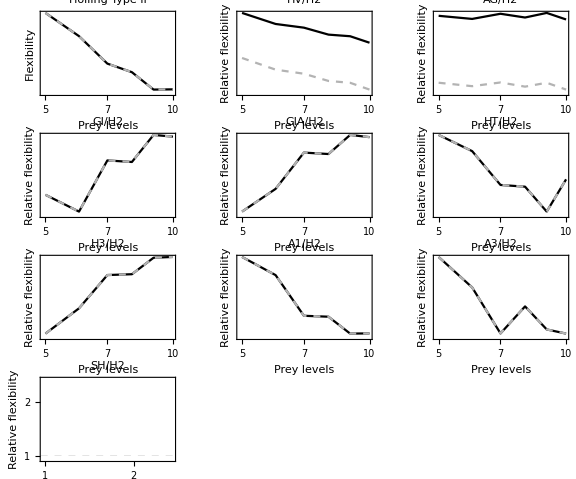

```mathematica
AllFixP2=
Legended[
GraphicsGrid[{
{p2fixH2,p2fixH2vHV,p2fixH2vAG},
{p2fixH2vGI,p2fixH2vGIA,p2fixH2vHT},
{p2fixH2vH3,p2fixH2vA1,p2fixH2vA3},
{p2fixH2vSH}
},
ImageSize-> Large],
Placed[
LineLegend[
Map[Directive,PlotStyleCols],
DeleteDuplicates[fixH1[[All,4]]],
LegendLabel->"Predator levels",
LegendLayout->"Row"],
Above]]
Export["GeomComp_fixP2.pdf",AllFixP2];
```

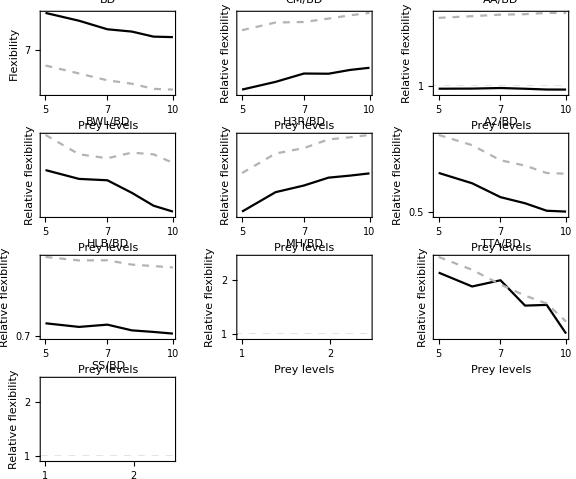

```mathematica
AllFixP3=
Legended[
GraphicsGrid[{
{p3fixBD,p3fixBDvCM,p3fixBDvAA},
{p3fixBDvBWL,p3fixBDvH3R,p3fixBDvA2},
{p3fixBDvHLB,p3fixBDvMH,p3fixBDvTTA},
{p3fixBDvSSS}
},
ImageSize-> Large],
Placed[
LineLegend[
Map[Directive,PlotStyleCols],
DeleteDuplicates[fixH1[[All,4]]],
LegendLabel->"Predator levels",
LegendLayout->"Row"],
Above]]
Export["GeomComp_fixP3.pdf",AllFixP3];
```